```mathematica
Fact[n_]:=If[n<0,"Error, n <0",If[n==0,1,n*Fact[n-1]]];
Fact[9]
```

362880

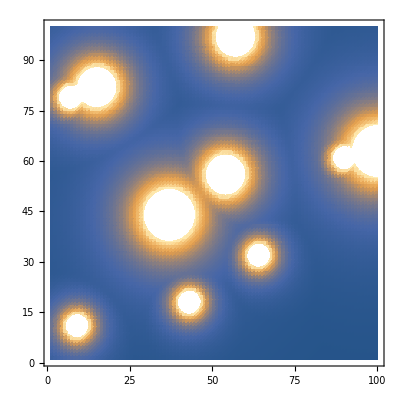

2610233

5037365

51.8174

```mathematica
c=Table[0,{100},{100}];
k=RandomSample[Range[100],20];
p1=100;
p2=300;
p3=500;
For[l=1,l≤5,l++,n=k[[l]];
m=k[[l+10]];
For[i=1,i≤100,i++,For[j=1,j≤100,j++,d=(n-i)^2+(m-j)^2;
If[d==0,c[[n,m]]=p1,p=p1/d;
If[p>c[[i,j]],c[[i,j]]=p]]]]];
For[l=6,l≤8,l++,n=k[[l]];
m=k[[l+10]];
For[i=1,i≤100,i++,For[j=1,j≤100,j++,d=(n-i)^2+(m-j)^2;
If[d==0,c[[n,m]]=p2,p=p2/d;
If[p>c[[i,j]],c[[i,j]]=p]]]]];
For[l=9,l≤10,l++,n=k[[l]];
m=k[[l+10]];
For[i=1,i≤100,i++,For[j=1,j≤100,j++,d=(n-i)^2+(m-j)^2;
If[d==0,c[[n,m]]=p3,p=p3/d;
If[p>c[[i,j]],c[[i,j]]=p]]]]];
ListDensityPlot[c]
sum=0;
People=Table[RandomInteger[{1,1000}],{100},{100}];
For[i=1,i≤100,i++,For[j=1,j≤100,j++,If[c[[i,j]]>1,sum+=People[[i,j]]]]]
sum
AllPeople=0;
For[i=1,i≤100,i++,For[j=1,j≤100,j++,AllPeople+=People[[i,j]]]];
AllPeople
procent=N[sum/AllPeople]*100
```

```mathematica
field=Table[0,{15},{15}];
field[[3,2]]=1;
field[[3,13]]=1;
field[[5,13]]=1;
field[[5,15]]=1;
field[[10,15]]=1;
field[[10,2]]=1;
MatrixPlot[field,Mesh->All]
findPos=0;
While[findPos≠1,m=RandomInteger[{1,15}];
For[j=1,j<15,j++,If[field[[m,j]]==1,n=j;
findPos=1;
Break[]]]]
startI=m;
startJ=n;
currentI=m;
currentJ=n;
r=1;l=0;u=0;d=0;
Print["Start"];
Print["(",currentI," ",currentJ,")"];
value=1;
delta=value;
While[True,(right) If[r==1,For[i=currentI;j=currentJ+1,j≤15,j++,If[field[[i,j]]==1,Print["(",i," ",j,")"];
currentJ=j;
currentI=i;
l=0;r=0;
u=1;d=1;
Break[]]]] (down) If[d==1,For[i=currentI+1;j=currentJ,i≤15,i++,If[field[[i,j]]==1,Print["(",i," ",j,")"];
currentJ=j;
currentI=i;
l=1;r=1;
u=0;d=0;
Break[]]]] (left) If[l==1,For[i=currentI;j=currentJ-1,j>1,j--,If[field[[i,j]]==1,Print["(",i," ",j,")"];
currentJ=j;
currentI=i;
l=0;r=0;
u=1;d=1;
Break[]]]] (up) If[u==1,For[i=currentI-1;j=currentJ,i>1,i--,If[field[[i,j]]==1,Print["(",i," ",j,")"];
currentJ=j;
currentI=i;
l=1;r=1;
u=0;d=0;
Break[]]]] If[startI==currentI&&startJ==currentJ,Break[]]]
```